# GWPEnsemble Package

Jeremy B. Maddox

Department of Chemistry and Biochemistry
Western Kentucky University
Bowling Green, KY 42101-1079
Email: jeremy.maddox@wku.edu

The GWPEnsemble package provides a self-contained framework for generating, propagating, and post-processing quantum trajectory ensembles within GWPTools. Given a GWPObject across the “1D”, “SS1D”, “MC1D”, or “2D” wavepacket engines, GWPEnsemble constructs structured initial coordinate grids using exact inverse-CDF quantile mapping, uniform spatial discretization, or Monte Carlo importance sampling. For time-dependent propagation, GWPEnsembleSolve integrates first-order kinematic (Bohmian guidance) or second-order dynamic (Newton–Bohm) equations of motion—either directly from a GWPObject or through user-supplied velocity and acceleration fields—while GWPEnsembleParse and GWPEnsembleFormat extract the underlying InterpolatingFunction time grids and reshape the resulting trajectory and derivative tensors for visualization and phase-space analysis.

## Loading the package

Load the core GWPTools package along with the engine, hydrodynamics, numerical potential, and GWPEnsemble extensions. (During active repository development, PacletDirectoryLoad points directly to the local working tree and is omitted once the compiled v1.0.1 paclet is installed.)

```mathematica
Needs["MaddoxScience`GWPTools`"]
Needs["MaddoxScience`GWPTools`GWPEngineSS1D`"]
Needs["MaddoxScience`GWPTools`GWPEngineMC1D`"]
Needs["MaddoxScience`GWPTools`GWPEngine2D`"]
Needs["MaddoxScience`GWPTools`GWPHydrodynamics`"]
Needs["MaddoxScience`GWPTools`GWPPhaseSpace`"]
Needs["MaddoxScience`GWPTools`GWPNumerical`"]
Needs["MaddoxScience`GWPTools`GWPEnsemble`"]
```

Verify that all four wavepacket engines are registered and that all subpackages have scrubbed their internal contexts, leaving only “MaddoxScience`GWPTools`” on $ContextPath:

```mathematica
GWP["Types"]
```

{1D,SS1D,MC1D,2D}

```mathematica
$ContextPath
```

{MaddoxScience`GWPTools`,System`,Global`}

Although GWPEnsemble loads backend dispatchers (GWP1DENSEMBLE, GWPSS1DENSEMBLE, GWPMC1DENSEMBLE, GWP2DENSEMBLE) and interpolation utilities (GWPExtractIFDATA), those symbols remain hidden inside GWPDeveloper. Only the four public-facing functions are exported into MaddoxScience`GWPTools` :

```mathematica
MaddoxScience`GWPTools`GWPDeveloper`GWPUsageTable[{GWPEnsemble,GWPEnsembleSolve,GWPEnsembleParse,GWPEnsembleFormat}]
```

Signature | Description
GWPEnsemble[GWPObject[], options] | Generates a structured phase-space or coordinate ensemble for the given wavepacket.
GWPEnsembleSolve[X0DAT, VFUN, {t, tMin, tMax}, opts] | Propagates a 1st-order kinematic ensemble.
GWPEnsembleSolve[X0DAT, V0DAT, AFUN, {t, tMin, tMax}, opts] | Propagates a 2nd-order dynamic ensemble.
GWPEnsembleSolve[GWPObject[], X0DAT, {t, tMin, tMax}, opts] | Automatically propagates Bohmian trajectories using the wavepacket's hydrodynamic velocity field.
GWPEnsembleParse[X0DAT, SOLN] | Extracts the exact interpolation grid and derivative tensors from NDSolve output.
GWPEnsembleFormat[ParsedData, key, opts] | Reshapes N-dimensional trajectory array data into standard paired lists for plotting.

## Single GWP Examples (1D)

For a 1D Gaussian wavepacket, GWPEnsemble provides four sampling strategies controlled via the “SamplingMethod”, “Grid”, “Time”, and WorkingPrecision options, which are demonstrated in the examples below.

### Default Behavior (Automatic Quantile Sampling)

We begin by initializing a default stationary wavepacket (α_0=1/4, x_0=0, p_0=0) which has initial position expectation value ⟨x⟩=0 and spatial width σ_x=1):

```mathematica
obj=GWP["1D"][];
```

Calling GWPEnsemble[obj] with no options triggers the default settings “SamplingMethod” → Automatic and “Grid”→ Automatic. For a 1D wavepacket, Automatic resolves to “UniformC” (uniform cumulative distribution sampling) and generates a N=100 point grid evaluated at the probability midpoints

c_k=(2k-1)/(2N)∈(0,1)

for k=1,2,…,N via the analytical inverse cumulative distribution function obj[“XC”][c,t]

100

{-√2 InverseErf[99/100],-√2 InverseErf[97/100],«97»,√2 InverseErf[99/100]}

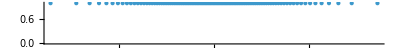

```mathematica
(*Default:100 equal-probability quantile points ("UniformC")*)
xdatDefault=GWPEnsemble[obj];
Length[xdatDefault]
Short[xdatDefault]
NumberLinePlot[xdatDefault]
```

### Uniform Spatial Grids (“UniformX”)

Selecting “SamplingMethod” → “UniformX” generates a uniformly spaced Cartesian coordinate grid centered around the wavepacket’s expectation value x_t=⟨x(t)⟩. The “Grid” option accepts three formats to control the number of grid points N and the spatial domain bounds:

“Grid” → N (or Automatic for N=100): Subdivides the default ±4 σ_x interval [x_t-4 σ_x,x+4 σ_x] into N evenly spaced points.

“Grid” → {N, “3Sigma”}: Subdivides the narrower ±3 σ_x interval [x_t-3 σ_x,x_t+3 σ_x] into N points.

“Grid” → {N, {xMin, xMax}}: Subdivides a user-specified coordinate window [x_min,x_max] into N points.

{-4,-28/9,-20/9,-4/3,-4/9,4/9,4/3,20/9,28/9,4}

{-3,-7/3,-5/3,-1,-1/3,1/3,1,5/3,7/3,3}

{0,2/9,4/9,2/3,8/9,10/9,4/3,14/9,16/9,2}

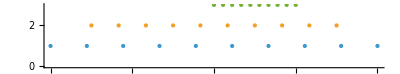

```mathematica
(*10 points across the default+/-4*Sigma window[-4,4]*)xdatX1=GWPEnsemble[obj,"SamplingMethod"->"UniformX","Grid"->10]
(*10 points across the+/-3*Sigma window[-3,3]*)
xdatX2=GWPEnsemble[obj,"SamplingMethod"->"UniformX","Grid"->{10,"3Sigma"}]
(*10 points across an explicit coordinate window[0,2]*)
xdatX3=GWPEnsemble[obj,"SamplingMethod"->"UniformX","Grid"->{10,{0,2}}]
NumberLinePlot[{xdatX1,xdatX2,xdatX3}]
```

### Equal-Probability Quantile Grids (“UniformC”)

Selecting “SamplingMethod” → “UniformC” places grid points at equal probability intervals along the cumulative distribution function

C(x)=∫_(-∞)^x ρ(x')ⅆ x'∈(0,1)

This naturally concentrates points near the peak of the probability density and spreading them out in the tails—making it ideal for equal-weight Bohmian trajectory ensembles:

“Grid” → N: Evaluates the inverse CDF at the N bin midpoints c_k=1/2N,3/2N,…,1-1/2N (avoiding the divergent endpoints at c=0 and c=1).

```mathematica
(*10 exact quantile points across the full distribution*)xdatC1=GWPEnsemble[obj,"SamplingMethod"->"UniformC","Grid"->10]
```

{-√2 InverseErf[9/10],-√2 InverseErf[7/10],-√2 InverseErf[1/2],-√2 InverseErf[3/10],-√2 InverseErf[1/10],√2 InverseErf[1/10],√2 InverseErf[3/10],√2 InverseErf[1/2],√2 InverseErf[7/10],√2 InverseErf[9/10]}

“Grid” → {N, {cMin, cMax}}: Subdivides the cumulative probability window [c_min,c_max]⊂(0,1) into N points including the endpoints.

```mathematica
(*10 exact quantile points restricted to the cumulative probability quartile[1/2,3/4]*)
xdatC2=GWPEnsemble[obj,"SamplingMethod"->"UniformC","Grid"->{10,{1/2,3/4}}]
```

{0,√2 InverseErf[1/18],√2 InverseErf[1/9],√2 InverseErf[1/6],√2 InverseErf[2/9],√2 InverseErf[5/18],√2 InverseErf[1/3],√2 InverseErf[7/18],√2 InverseErf[4/9],√2 InverseErf[1/2]}

### Stochastic Sampling (“Random” vs. “RandomDensity”)

GWPEnsemble provides two distinct random sampling modes for 1D wavepackets:

“SamplingMethod” → “Random”: Draws N sorted variates directly from the analytical unbounded Gaussian distribution NormalDistribution[obj[“RX”][t], obj[“UX”][t]] over (-∞,∞). Note that “Random” only reads the point count N from “Grid” and ignores spatial bound specifications.

```mathematica
(*10 sorted random variates from the full unbounded normal distribution*)xdatR1=GWPEnsemble[obj,"SamplingMethod"->"Random","Grid"->10]
```

{-1.45002,-1.2273,-0.524906,0.2578,0.404352,1.09111,1.36425,1.42091,1.54276,1.67}

“SamplingMethod” → “RandomDensity”: Constructs a numerical ProbabilityDistribution from the wavepacket density obj[“RHO”][x,t] truncated and normalized over a bounded spatial domain (±4 σ_x by default, “3Sigma”, or an explicit {xMin, xMax} window).

```mathematica
(*10 sorted random variates restricted to the+/-3*Sigma window[-3,3]*)
xdatRD1=GWPEnsemble[obj,"SamplingMethod"->"RandomDensity","Grid"->{10,"3Sigma"}]
(*10 sorted random variates restricted to the positive spatial window[0,2]*)
xdatRD2=GWPEnsemble[obj,"SamplingMethod"->"RandomDensity","Grid"->{10,{0,2}}]
```

{-1.85671,-0.650987,-0.430681,-0.316094,-0.214369,-0.174862,0.0874585,0.467093,0.65863,0.784336}

{0.0364545,0.0441243,0.168528,0.26206,0.292241,0.445252,0.506453,0.6206,0.974639,1.29136}

### Controlling Numerical Precision (WorkingPrecision)

By default (WorkingPrecision → Automatic), “Random” and “RandomDensity” generate machine-precision floating-point numbers, whereas exact methods (“UniformX” and “UniformC”) preserve exact symbolic expressions when the underlying wavepacket parameters are exact. Passing an explicit WorkingPrecision→ d option overrides this default across all sampling methods—generating arbitrary-precision random variates or directly evaluating exact symbolic grids to d digits:

```mathematica
(*Arbitrary-precision random sampling (25 digits)*)xdatR25=GWPEnsemble[obj,"SamplingMethod"->"Random","Grid"->5,WorkingPrecision->25]

xdatRD25=GWPEnsemble[obj,"SamplingMethod"->"RandomDensity","Grid"->{5,{0,2}},WorkingPrecision->25]

(*Evaluating an exact symbolic quantile grid ("UniformC") directly to 25-digit precision*)
xdatC25=GWPEnsemble[obj,"SamplingMethod"->"UniformC","Grid"->5,WorkingPrecision->25]
```

{-1.687629985363464712124182,-0.5795184771545846187283321,0.037428786971671754335488,0.5990531394879662210480382,1.775701598614059580037721}

{0.1398126705513906114004288,0.1564264296515692707520394,0.453194607537803516456834,0.8397327066161624067498137,1.685541209592374187077229}

{-1.281551565544600466965103,-0.5244005127080407840382893,0,0.5244005127080407840382893,1.281551565544600466965103}

### Visual Comparison & Time-Evolved Ensembles (“Time”)

We can visually compare the point distributions of “UniformX”, “UniformC”, and “Random” (for N=25) against the underlying Gaussian probability density ρ(x) and the cumulative distribution C(x):

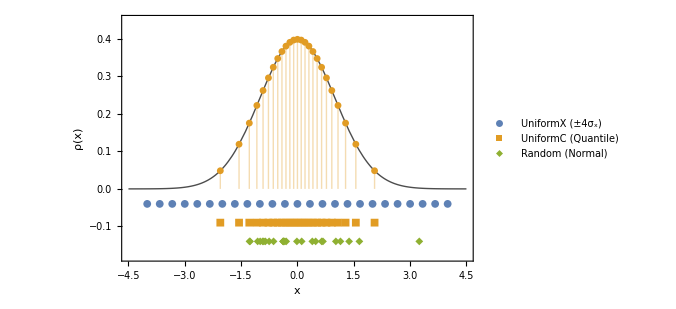

```mathematica
ensX=GWPEnsemble[obj,"SamplingMethod"->"UniformX","Grid"->25];
ensC=GWPEnsemble[obj,"SamplingMethod"->"UniformC","Grid"->25];
ensR=GWPEnsemble[obj,"SamplingMethod"->"Random","Grid"->25];

Show[
Plot[obj["RHOX"][x],{x,-4.5,4.5},PlotRange->{{-4.5,4.5},{-0.18,0.45}},Frame->True,FrameLabel->{"x","ρ(x)"},PlotStyle->Directive[Thick,GrayLevel[0.3]],BaseStyle->{FontSize->12},ImageSize->500],ListPlot[{Thread[{ensX,-0.04}],Thread[{ensC,-0.09}],Thread[{ensR,-0.14}]},PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3]},PlotMarkers->{Automatic,8},PlotLegends->{"UniformX (±4σ_x)","UniformC (Quantile)","Random (Normal)"}],(*Project UniformC markers directly onto the density curve to highlight peak clustering*)ListPlot[Transpose[{ensC,obj["RHOX"][ensC]}],Filling->Axis,FillingStyle->Directive[Opacity[0.35],ColorData[97,2]],PlotStyle->ColorData[97,2],PlotMarkers->{Automatic,7}]]
```

When a GWPObject is initialized with a “Potential” model, passing the “Time” → t option (default 0) instructs GWPEnsemble to propagate the wavepacket parameters to time t prior to generating the coordinate ensemble.   Below, we initialize a squeezed, displaced wavepacket (α_0=1/2, x_0=-2, p_0=0) in a harmonic oscillator (“Potential” → “HO”) and sample its 15-point quantile ensemble at t=0, t=π/2 (origin crossing with compressed width), and t=π (right turning point):

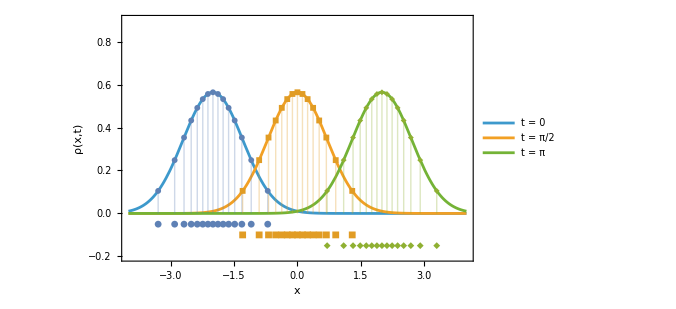

```mathematica
objDyn=GWP["1D"][1/2,-2,0,"Potential"->"HO"];
ensT0=GWPEnsemble[objDyn,"SamplingMethod"->"UniformC","Grid"->15,"Time"->0];
ensT1=GWPEnsemble[objDyn,"SamplingMethod"->"UniformC","Grid"->15,"Time"->Pi/2];
ensT2=GWPEnsemble[objDyn,"SamplingMethod"->"UniformC","Grid"->15,"Time"->Pi];

Show[
Plot[{
objDyn["RHOX"][x,0],
objDyn["RHOX"][x,Pi/2],
objDyn["RHOX"][x,Pi]},{x,-4,4},
PlotRange->{{-4,4},{-0.2,0.9}},Frame->True,FrameLabel->{"x","ρ(x,t)"},PlotLegends->{"t = 0","t = π/2","t = π"},BaseStyle->{FontSize->12},ImageSize->500],(*Color-matched rug markers below the axis+density-curve markers*)
ListPlot[{
Thread[{ensT0,-0.05}],
Thread[{ensT1,-0.10}],
Thread[{ensT2,-0.15}]},
PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3]},PlotMarkers->{Automatic,7}],
ListPlot[{
Transpose[{ensT0,objDyn["RHOX"][ensT0,0]}],Transpose[{ensT1,objDyn["RHOX"][ensT1,Pi/2]}],Transpose[{ensT2,objDyn["RHOX"][ensT2,Pi]}]},
Filling->Axis,PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3]},PlotMarkers->{Automatic,6}]]
```

## Superposition Examples (SS1D and MC1D)

For two-state (SS1D) and multi-component (MC1D) superpositions, quantum interference between overlapping Gaussian branches produces oscillatory nodes and fringes in the probability density ρ(x,t). Consequently, the cumulative distribution function C(x) cannot be inverted analytically in closed form.

### Sampling Methods for SS1D and MC1D

Both SS1D and MC1D share an identical GWPEnsemble interface with three sampling methods:

“UniformX” (or “Cartesian” / Automatic): Subdivides the composite ±4 σ_x bounding box [min_k (x_k-4 σ_k),max_k (x_k+4 σ_k)] (or a user-supplied {N, {xMin, xMax}} window) into N evenly spaced points.

“InverseC” (Numerical Quantile Root-Finding): Solves C(x_k)=c_k sequentially across the quantile grid using FindRoot supplied with the exact analytical Jacobian ∂_x C(x,t)=ρ(x,t). Any standard FindRoot options (such as WorkingPrecision, AccuracyGoal, or MaxIterations) may be passed directly into GWPEnsemble.

“RandomDensity” (Rejection Sampling): Generates N sorted variates via von Neumann rejection sampling under a bounding envelope of the interfering probability density.

### Antisymmetric Two-Sate Superposition (“SS1D”)

Here we initialize an antisymmetric two-Gaussian superposition (“C” → -1) with overlapping branches centered at x_0=±1/2 with α_0=1, creating a destructive interference node at x=0. Comparing “UniformX”, “InverseC”, and “RandomDensity” demonstrates how both “InverseC” and “RandomDensity” automatically evacuate the destructive node at the origin and cluster trajectories inside the two constructive interference lobes:

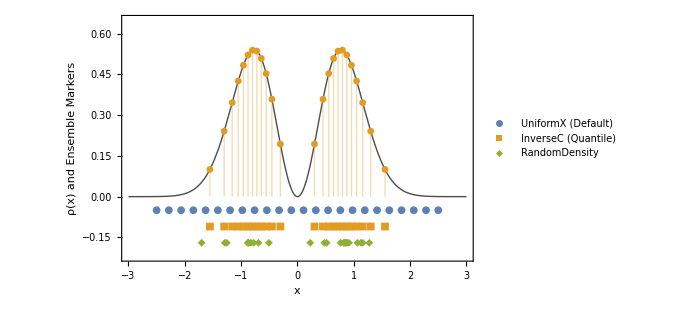

```mathematica
(*Antisymmetric overlapping two-state superposition with a node at x=0*)objSS=GWP["SS1D"][{1,1},{-1/2,1/2},"C"->-1];

ensSSX=GWPEnsemble[objSS,"SamplingMethod"->"UniformX","Grid"->24];
ensSSC=GWPEnsemble[objSS,"SamplingMethod"->"InverseC","Grid"->24];
ensSSRD=GWPEnsemble[objSS,"SamplingMethod"->"RandomDensity","Grid"->24];

Show[
Plot[objSS["RHOX"][x],{x,-3,3},PlotRange->{{-3,3},{-0.22,0.65}},Frame->True,FrameLabel->{"x","ρ(x) and Ensemble Markers"},PlotStyle->Directive[Thick,GrayLevel[0.3]],BaseStyle->{FontSize->12},ImageSize->500],
ListPlot[{
Thread[{ensSSX,-0.05}],
Thread[{ensSSC,-0.11}],
Thread[{ensSSRD,-0.17}]},PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3]},PlotMarkers->{Automatic,8},PlotLegends->{"UniformX (Default)","InverseC (Quantile)","RandomDensity"}],(*Project InverseC points onto rho(x) to highlight evacuation of the x=0 node*)ListPlot[Transpose[{ensSSC,objSS["RHOX"][ensSSC]}],Filling->Axis,FillingStyle->Directive[Opacity[0.35],ColorData[97,2]],PlotStyle->ColorData[97,2],PlotMarkers->{Automatic,7}]]
```

Because “InverseC” delegates directly to FindRoot with the exact analytical derivative ∂_x C(x)=ρ(x), arbitrary-precision quantile grids or restricted probability windows {N, {cMin, cMax}} can be computed simply by passing FindRoot options:

```mathematica
(*8 high-precision quantile points across the upper lobe c in[0.55,0.95]*)GWPEnsemble[objSS,"SamplingMethod"->"InverseC","Grid"->{8,{11/20,19/20}},WorkingPrecision->25]
```

{0.4166714417144559978882354,0.5620715770260045022333807,0.6774356738019457344060837,0.7840498768577462785309404,0.8915416102667971546290031,1.00868940568518187224394,1.149856025628348069500381,1.356921631288726240784366}

### Multi-Component Focal Interference (“MC1D”)

In this dynamic “MC1D” example, a train of three Gaussian wavepackets (α_0=1) initialized at x_0∈{-3,0,3} in a harmonic oscillator (“Potential” → “HO”) are sampled via “InverseC” (N=30) at t=0 (three well-separated Gaussian peaks) and at the half-period focal collision t=π/2 (where all three branches cross at the origin to form high-frequency three-beam interference fringes):

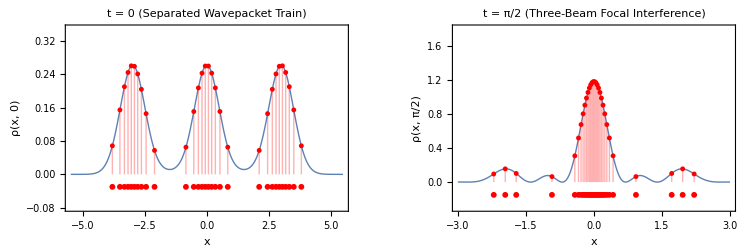

```mathematica
objMC=GWP["MC1D"][{1,1,1},{-3,0,3},"C"->{1,1,1},"Potential"->"HO"];

(*30 quantile points at t=0 (separated lobes) vs.t=Pi/2 (focal interference)*)
ensMC0=GWPEnsemble[objMC,"SamplingMethod"->"InverseC","Grid"->30,"Time"->0];
ensMCT=GWPEnsemble[objMC,"SamplingMethod"->"InverseC","Grid"->30,"Time"->Pi/2];

GraphicsRow[{Show[Plot[objMC["RHOX"][x,0],{x,-5.5,5.5},PlotRange->{{-5.5,5.5},{-0.08,0.35}},Frame->True,FrameLabel->{"x","ρ(x, 0)"},PlotLabel->"t = 0 (Separated Wavepacket Train)",PlotStyle->Directive[Thick,ColorData[97,1]],BaseStyle->{FontSize->11}],ListPlot[Thread[{ensMC0,-0.03}],PlotStyle->Red,PlotMarkers->{Automatic,6}],ListPlot[Transpose[{ensMC0,objMC["RHOX"][ensMC0,0]}],Filling->Axis,FillingStyle->Directive[Opacity[0.3],Red],PlotStyle->Red,PlotMarkers->{Automatic,5}]],Show[Plot[objMC["RHOX"][x,Pi/2],{x,-3,3},PlotRange->{{-3,3},{-0.3,1.8}},Frame->True,FrameLabel->{"x","ρ(x, π/2)"},PlotLabel->"t = π/2 (Three-Beam Focal Interference)",PlotStyle->Directive[Thick,ColorData[97,1]],BaseStyle->{FontSize->11}],ListPlot[Thread[{ensMCT,-0.15}],PlotStyle->Red,PlotMarkers->{Automatic,6}],ListPlot[Transpose[{ensMCT,objMC["RHOX"][ensMCT,Pi/2]}],Filling->Axis,FillingStyle->Directive[Opacity[0.3],Red],PlotStyle->Red,PlotMarkers->{Automatic,5}]]},ImageSize->750]
```

## Single GWP Examples (2D)

For two-dimensional wavepackets (“2D”), GWPEnsemble generates lists of coordinate pairs {{x1, y1}, {x2, y2}, ...} adapted to the position center μ=(x_t,y_t)^T and 2×2 spatial covariance matrix Σ_r of the wavepacket.

### Sampling Methods & Grid Specifications Overview

Five “SamplingMethod” geometries are available for 2D wavepackets:

“Cartesian” (or “UniformX” / Automatic): Forms a rectangular n_x×n_y outer-product grid across [x_t-4 σ_x,x_t+4 σ_x]×[y_t-4 σ_y,y_t+4 σ_y] (or custom bounds).

“AffineC”: Warps a canonical n_x×n_y normal quantile mesh via the Cholesky factor L of the covariance matrix (Σ_r=L L^T) to align with the wavepacket’s principal axes and tilt.

“PolarC”: Maps n_r radial probability shells and n_θ angular rays onto concentric constant-probability ellipses via the polar inverse CDF obj[“XC”][cr, ctheta].

“Random”: Draws N=n_x n_y variates directly from the analytical MultinormalDistribution[mu, sigma].

“RandomDensity”: Draws N variates via 2D numerical rejection sampling over the bounding box.

For a “2D” wavepacket, the “Grid” option accepts three flexible formats:

“Grid” → Automatic: Defaults to a 20×20 mesh (400 total points).

“Grid”→ N (single integer): Sets the total point count to N for random methods (“Random” and “RandomDensity”), or constructs an approximately square √N×√N mesh for structured grid methods.

“Grid” → {nx, ny} or {nx, ny, {{xMin, xMax}, {yMin, yMax}}}: Explicitly specifies the grid dimensions n_x×n_y (or n_r×n_θ radial shells and angular rays for “PolarC”), along with optional custom bounding intervals for “Cartesian” and “RandomDensity”.

### Structured Covariance-Adapted Meshes (“AffineC” and “PolarC”)

“AffineC” (Cholesky Quantile Mesh): 

For a correlated 2D Gaussian wavepacket, the spatial probability density ρ(x,y) does not factorize along the laboratory x and y axes, meaning independent 1D quantile grids cannot capture its tilted covariance ellipse. To construct an exact equal-probability mesh without numerical root-finding, “AffineC” first generates an uncorrelated n_x×n_y canonical quantile grid z=(z_x,z_y)^T for a 2D standard normal distribution (μ_z=(0,0)^T, Σ_z=I_2) by evaluating the 1D inverse cumulative distribution function z_k=√2 erf^-1(2 c_k-1) at the probability midpoints c_k∈(0,1) along each axis. Next, it computes the lower-triangular Cholesky decomposition L of the wavepacket’s 2×2 spatial covariance matrix Σ_r=L L^T and applies the affine transformation r=μ+L z to every canonical point z. Geometrically, L scales and shears the rectangular unit-normal quantile mesh so that it aligns with the principal axes and correlation tilt of the physical wavepacket centered at μ=(x_t,y_t)^T.

“PolarC” (Radial-Angular Quantile Shells): 

Rather than warping a rectangular grid, “PolarC” samples the 2D Gaussian probability distribution in canonical polar quantile coordinates (c_r,c_θ)∈[0,1)×[0,1). For a grid specification of n_r radial shells and n_θ angular rays, the method places radial cumulative probability coordinates at uniform intervals (c_(r,i)=i/(n_r+1) for  i=1,…,n_r) and distributes n_θ angular phase coordinates uniformly around each shell (c_(θ,j)=j/n_θ for j=0,…,n_θ-1).  When “Structure” → “Staggered” (the default) is active, odd-numbered radial shells are shifted in angular phase by half a ray spacing (Δc_θ=1/2 n_θ) to create a triangulated packing, whereas “Aligned” keeps all points along fixed radial spokes. If “IncludeCore” → True (the default), the origin point (c_r,c_θ)=(0,0) is prepended to the ensemble. Finally, each (c_r,c_θ) pair is mapped through the backend 2D polar inverse cumulative distribution (GWP2DXC), which converts (c_r,c_θ) into canonical polar coordinates (ρ=√(-2ln(1-c_r)), ϕ=2π c_θ) and transforms them onto concentric constant-probability ellipses aligned with the wavepacket’s covariance matrix Σ_r and center μ.

### Comparing 2D Sampling Geometries

To illustrate how the structured quantile methods adapt to anisotropic squeezing and inter-mode correlation, we construct a 2D wavepacket centered at r_0=(1,-1) with a non-diagonal shape matrix:

A_0=(1 | 3/5
3/5 | 1/2)

```mathematica
(*Anisotropic,correlated 2D GWP tilted in the xy-plane*)
obj2D=GWP["2D"][{{1,3/5},{3/5,1/2}},{1,-1}];

ptsCart=GWPEnsemble[obj2D,"SamplingMethod"->"Cartesian","Grid"->{12,12}];
ptsAffine=GWPEnsemble[obj2D,"SamplingMethod"->"AffineC","Grid"->{12,12}];
ptsPolar=GWPEnsemble[obj2D,"SamplingMethod"->"PolarC","Grid"->{6,24}]; (*6*24+1 core=145 pts*)
ptsRand=GWPEnsemble[obj2D,"SamplingMethod"->"Random","Grid"->144];
```

Visualizing all four ensembles superimposed on the contour plot of the 2D probability density ρ(x,y) illustrates how “AffineC” and “PolarC” shear and rotate automatically with the covariance ellipse, whereas “Cartesian” remains locked to the laboratory axes:

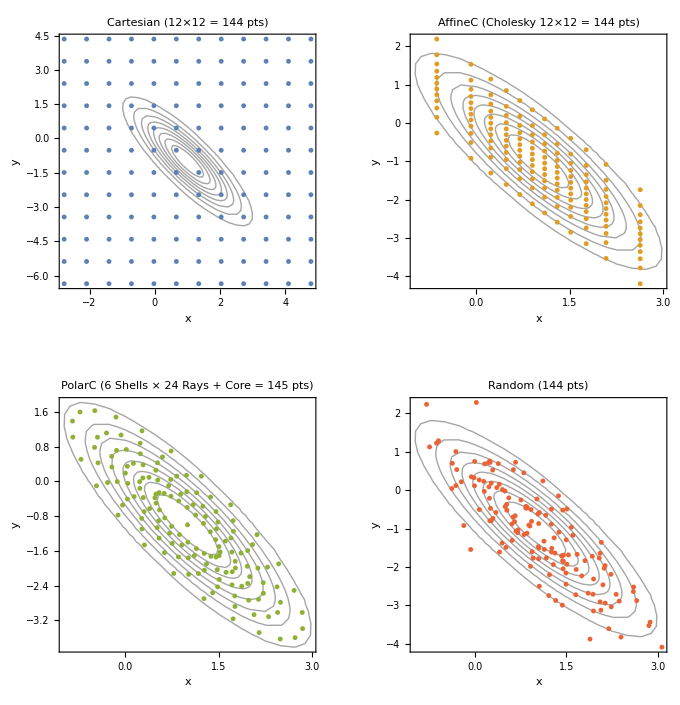

```mathematica
bgContour=ContourPlot[obj2D["RHOX"][x,y],{x,-2.5,4.5},{y,-5,3},PlotRange->All,Contours->8,ContourShading->None,ContourStyle->Directive[Thin,GrayLevel[0.65]],Frame->True,FrameLabel->{"x","y"},BaseStyle->{FontSize->11}];

GraphicsGrid[{{Show[bgContour,ListPlot[ptsCart,PlotStyle->ColorData[97,1],PlotMarkers->{Automatic,5}],PlotLabel->"Cartesian (12×12 = 144 pts)"],Show[bgContour,ListPlot[ptsAffine,PlotStyle->ColorData[97,2],PlotMarkers->{Automatic,5}],PlotLabel->"AffineC (Cholesky 12×12 = 144 pts)"]},{Show[bgContour,ListPlot[ptsPolar,PlotStyle->ColorData[97,3],PlotMarkers->{Automatic,5}],PlotLabel->"PolarC (6 Shells × 24 Rays + Core = 145 pts)"],Show[bgContour,ListPlot[ptsRand,PlotStyle->ColorData[97,4],PlotMarkers->{Automatic,5}],PlotLabel->"Random (144 pts)"]}},ImageSize->680]
```

### “PolarC” Shell Layout Options (“Structure” and “IncludeCore”)

The “PolarC” method supports two specialized layout options that control the arrangement of points across the concentric probability shells:

“Structure” → “Staggered” (default) vs. “Aligned”: “Staggered” alternates the angular phase of adjacent radial shells by half a ray spacing (Δc_θ=1/2 n_θ), producing a triangulated packing, whereas “Aligned” places points along fixed radial spokes.

“IncludeCore” → True (default) vs. False: Controls whether the wavepacket center μ=(x_t,y_t)^T corresponding to (c_r,c_θ)=(0,0) is prepended as a core point at the center of the innermost ring.

Because “PolarC” places each radial shell at a uniform cumulative probability step and distributes rays at uniform canonical phase angles, the sampling geometry defines a natural curvilinear polar mesh adapted to the wavepacket’s covariance ellipse. In the figure below, we set the background contour levels to match the five radial shells and draw radial spokes from the wavepacket center along the 16 canonical ray angles. This makes the structural difference immediately clear: the “Aligned” ensemble places every marker directly at the intersection of a spoke and a contour ring, whereas the “Staggered” ensemble shifts alternating rings halfway between the spokes for a more uniform spatial packing:

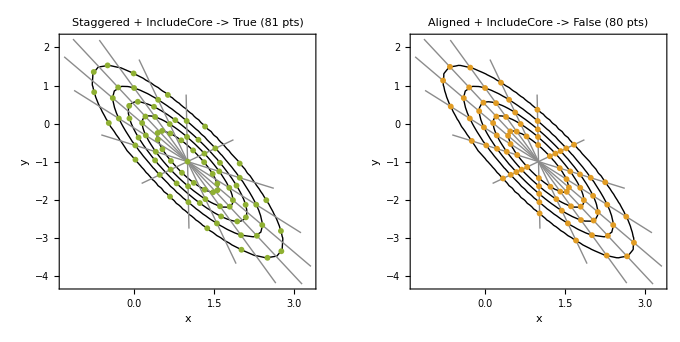

```mathematica
(*Compare Staggered (with core:5*16+1=81 pts) vs.Aligned (without core:5*16=80 pts)*)polarStaggered=GWPEnsemble[obj2D,"SamplingMethod"->"PolarC","Grid"->{5,16},"Structure"->"Staggered","IncludeCore"->True];

polarAligned=GWPEnsemble[obj2D,"SamplingMethod"->"PolarC","Grid"->{5,16},"Structure"->"Aligned","IncludeCore"->False];

(*1. Exact density contour levels for the nr=5 radial shells*)
nr=5;
ntheta=16;
rhoMax=obj2D["RHOX"][1,-1];
crContours=rhoMax*(1-Range[nr]/(nr+1));

(*2. Radial spokes from the center {1,-1} out to cr=0.95 along the 16 ray angles*)
spokeTips=Table[obj2D["XC"][0.95,j/ntheta],{j,0,ntheta-1}];
spokeGraphics=Graphics[{Thin,GrayLevel[0.55],Line[Table[{{1,-1},pt},{pt,spokeTips}]]}];

bgContourPolar=Show[ContourPlot[obj2D["RHOX"][x,y],{x,-2.5,4.5},{y,-5,3},PlotRange->All,Contours->crContours,ContourShading->None,ContourStyle->Thin,Frame->True,FrameLabel->{"x","y"},BaseStyle->{FontSize->11}],spokeGraphics];

GraphicsRow[{Show[bgContourPolar,ListPlot[polarStaggered,PlotStyle->ColorData[97,3],PlotMarkers->{Automatic,6}],PlotLabel->"Staggered + IncludeCore -> True (81 pts)"],Show[bgContourPolar,ListPlot[polarAligned,PlotStyle->ColorData[97,2],PlotMarkers->{Automatic,6}],PlotLabel->"Aligned + IncludeCore -> False (80 pts)"]},ImageSize->680]
```

## Dynamic Trajectory Propagation

Once an initial coordinate grid X0DAT is generated with GWPEnsemble, time-dependent trajectories are integrated, parsed, and reshaped for visualization directly within GWPEnsemble using a three-stage functional pipeline:

GWPEnsembleSolve — Integrates 1st-order kinematic (Bohmian guidance) or 2nd-order dynamic (Newton–Bohm) ODE systems over arbitrary N-dimensional ensemble arrays, or accepts a GWPObject directly to propagate Bohmian trajectories automatically.

GWPEnsembleParse — Inspects the internal structure of the resulting InterpolatingFunction list to extract the adaptive solver time grid “TDAT”, the position tensor “X0DAT”, and the velocity tensor “X1DAT” without redundant function evaluations.

GWPEnsembleFormat — Reshapes and slices the parsed trajectory tensors into ListLinePlot-ready time series or parametric configuration-space orbits using the “Component” and “PairWithTime” options.

### Solver Signatures & Formatting Options

GWPEnsembleSolve supports three primary calling conventions depending on whether the velocity or acceleration field is taken directly from a GWPObject or supplied as a custom function:

Direct GWPObject Bohmian Propagation (1st-Order):

GWPEnsembleSolve[obj, X0DAT, {t, tMin, tMax}, opts] automatically extracts the hydrodynamic velocity field from obj and integrates ẋ(t)=v(x,t).

Custom Kinematic Velocity Field (1st-Order):

GWPEnsembleSolve[X0DAT, VFUN, {t, tMin, tMax}, opts] integrates ẋ(t)=VFUN[x(t),t] for a two-argument velocity function Function[{x, t}, ...].

Dynamic Acceleration Field (2nd-Order Newton–Bohm):

GWPEnsembleSolve[X0DAT, V0DAT, AFUN, {t, tMin, tMax}, opts] integrates x^(..)(t)=AFUN[x(t),ẋ(t),t] given initial positions X0DAT, initial velocities V0DAT, and a two-argument acceleration function Function[{x, t}, ...]. Any standard NDSolve options (such as Method, WorkingPrecision, MaxSteps, or AccuracyGoal) may be passed directly to GWPEnsembleSolve

Once parsed via PARSED = GWPEnsembleParse[X0DAT, SOLN], trajectories are formatted for plotting with GWPEnsembleFormat[PARSED, key, opts], where key is “X0DAT” (positions, the default) or “X1DAT” (velocities):

“Component” → All | k | {k1, k2, ...}: Selects which spatial coordinate component(s) to extract for multi-dimensional ensembles (defaults to All).

“PairWithTime” -> Automatic | True | False: Controls whether the output coordinates are paired with the solver time grid as {t, x_k(t)} curves (default True for 1D data or single components) or returned as parametric configuration-space orbits {x(t), y(t)} (default False when multiple spatial components are extracted).

### Squeezed & Displaced Harmonic Oscillator (Affine Breathing + Oscillation)

A single 1D Gaussian wavepacket displaced from equilibrium with an initial width narrower than the ground state exhibits classical center-of-mass sloshing combined with quantum width breathing at 2ω. Because the single-Gaussian Bohmian velocity field is strictly linear in x, the quantile trajectories form a non-crossing affine fan that expands and contracts in lockstep with the analytical standard deviation envelope.

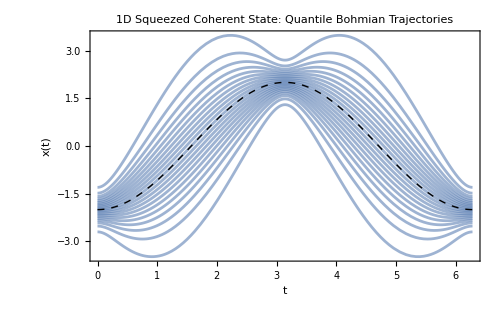

```mathematica
(*Displaced (x0=-2) and squeezed (a0=2) 1D harmonic oscillator*)
obj1D=GWP["1D"][2,-2,0,"Potential"->"HO"];

(*Sample 21 equiquantile initial positions via UniformC*)
x0=GWPEnsemble[obj1D,"SamplingMethod"->"UniformC","Grid"->21,"Time"->0];

(*Propagate 1st-order Bohmian trajectories directly from obj1D over one full period[0,2 Pi]*)
(*Note:Equivalent to GWPEnsembleSolve[x0,Function[{x,t},obj1D["VX"][x,t]],{t,0,2 Pi}]*)
sol1D=GWPEnsembleSolve[obj1D,x0,{t,0,2 Pi}];
parsed1D=GWPEnsembleParse[x0,sol1D];
traj1D=GWPEnsembleFormat[parsed1D,"X0DAT"];

(*Plot trajectories alongside the classical center RX(t)*)
Show[ListLinePlot[traj1D,PlotStyle->Directive[Opacity[0.6],ColorData[97,1]],Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"1D Squeezed Coherent State: Quantile Bohmian Trajectories",BaseStyle->{FontSize->11},ImageSize->500],Plot[obj1D["RX"][t],{t,0,2 Pi},PlotStyle->Directive[Black,Dashed,Thick]]]
```

### Second-Order Newton-Bohm Propagation (Classical+Quantum Force)

Alternatively, trajectories can be integrated using the second-order Newton–Bohm equation of motion, where each particle is accelerated by the sum of the external classical force (“FEX”) and the Bohmian quantum force (“QFX”). When initialized with the exact hydrodynamic velocity field v0 = obj1D[“VX”][x0, 0], second-order dynamic propagation reproduces the first-order Bohmian trajectories to numerical precision:

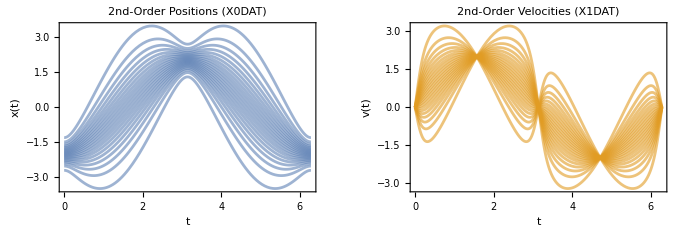

```mathematica
(*1. Initial positions x0 and initial Bohmian velocities v0 at t=0*)x0=GWPEnsemble[obj1D,"SamplingMethod"->"UniformC","Grid"->21,"Time"->0];
v0=obj1D["VX"][x0,0];

(*2. Define total acceleration a(x,t)=(F_external+F_quantum)/m (with m=1)*)
aFun=Function[{x,t},Evaluate[obj1D["FEX"][x,t]+obj1D["QFX"][x,t]]];

(*3. Integrate 2nd-order Newton-Bohm equations and parse X0DAT and X1DAT*)
sol1DDyn=GWPEnsembleSolve[x0,v0,aFun,{t,0,2 Pi}];
parsed1DDyn=GWPEnsembleParse[x0,sol1DDyn];

trajPos=GWPEnsembleFormat[parsed1DDyn,"X0DAT"];
trajVel=GWPEnsembleFormat[parsed1DDyn,"X1DAT"];

(*4. Visualize 2nd-order position x(t) and velocity v(t)*)
GraphicsRow[{ListLinePlot[trajPos,PlotStyle->Directive[Opacity[0.6],ColorData[97,1]],Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"2nd-Order Positions (X0DAT)"],ListLinePlot[trajVel,PlotStyle->Directive[Opacity[0.6],ColorData[97,2]],Frame->True,FrameLabel->{"t","v(t)"},PlotLabel->"2nd-Order Velocities (X1DAT)"]},ImageSize->680]
```

### Anisotropic Coupled 2D Oscillator (Lissajous Swirl & Phase-Space Vorticity)

Applying “SamplingMethod” → “PolarC” to a 2D Gaussian wavepacket with initial off-diagonal correlation (α_xy=1) and transverse momentum demonstrates how GWPEnsembleSolve propagates multi-dimensional ensembles directly from obj2D, and how GWPEnsembleFormat extracts both 2D planar orbits {x(t), y(t)} and 1D coordinate time series {t, x(t)} and {t, y(t)}:

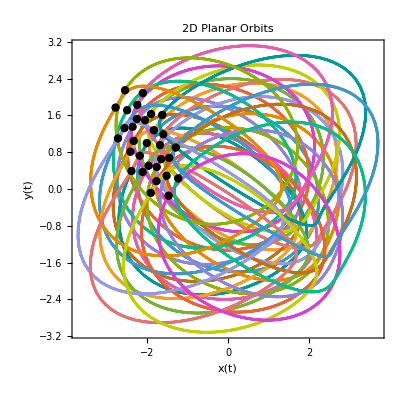

-Graphics3D-

```mathematica
(*1. Correlated 2D Gaussian in an isotropic harmonic trap*)obj2D=GWP["2D"][{{3/2,1/2},{1/2,2/3}},{-2,1},{1,3/2},"Potential"->"HO"];

(*2. Sample 3 radial shells x 10 angular rays+1 core point=31 trajectories*)
xy0=GWPEnsemble[obj2D,"SamplingMethod"->"PolarC","Grid"->{3,10},"Time"->0];

(*3. Propagate 2D Bohmian velocity field directly from obj2D*)
sol2D=GWPEnsembleSolve[obj2D,xy0,{t,0,2*2 Pi}];
parsed2D=GWPEnsembleParse[xy0,sol2D];

(*4. Extract planar (x,y) orbits and 1D x(t),y(t) projections*)
trajXY=GWPEnsembleFormat[parsed2D,"X0DAT"];
trajX=GWPEnsembleFormat[parsed2D,"X0DAT","Component"->1];
trajY=GWPEnsembleFormat[parsed2D,"X0DAT","Component"->2];

GraphicsRow[{ListLinePlot[trajXY,AspectRatio->1,Frame->True,FrameLabel->{"x(t)","y(t)"},PlotLabel->"2D Planar Orbits",Epilog->{PointSize[0.015],Black,Point[xy0]}],GraphicsColumn[{ListLinePlot[trajX,Frame->True,FrameLabel->{"t","x(t)"},PlotRange->{-4,4}],ListLinePlot[trajY,Frame->True,FrameLabel->{"t","y(t)"},PlotRange->{-4,4}]}]},ImageSize->750]

(*Prepend TDAT to each {x(t),y(t)} pair to visualize 3D spacetime worldlines {t,x(t),y(t)}*)
trajTXY=MapThread[Prepend,{#,parsed2D["TDAT"]}]&/@trajXY;

ListLinePlot3D[trajTXY,BoxRatios->{3,1,1},PlotStyle->Directive[ColorData[97,1],Thin],AxesLabel->{"t","x(t)","y(t)"},PlotLabel->"3D Spacetime Worldlines",ImageSize->550]
```

### Laser-Driven “Schrödinger’s Cat” Superposition (MC1D + Chirped Pulse)

A two-packet MC1D superposition starts separated in a harmonic trap (x_0={-5/2,5/2}) and is hit by an ultrashort Gaussian-envelope laser pulse

V_1(t)=E_0 ⅇ^(-(t-t_0)^2/τ^2)cos(ω_L t)

As the two branches collide and interfere, the Bohmian trajectories undergo sharp non-crossing topological bounces between the interference fringes while the entire interference pattern is shaken by the laser field. Separating the DensityPlot overlay from a standalone trajectory plot highlights the fine-scale channel structure:

```mathematica
(*1. Define a Gaussian-envelope oscillating laser pulse (dipole force v1[t])*)GWPClearCache["Quiet"];
Clear[v0Pulse,v1Pulse,v2Pulse];
v0Pulse[t_]:=0;
v1Pulse[t_]:=2.5*Exp[-(t-Pi)^2/0.8^2]*Cos[4 t];
v2Pulse[t_]:=1; (*Harmonic confinement omega=1*)

(*2. Build a 2-state Cat superposition driven by the numerical pulse over[0,2 Pi]*)
objCat=GWP["MC1D"][{1,1},{-5/2,5/2},{0,0},"C"->{1,1},"Potential"->{"Numerical",v0Pulse,v1Pulse,v2Pulse,0,2 Pi}];

(*3. Sample 30 quantile trajectories across the bimodal initial density*)
x0Cat=GWPEnsemble[objCat,"SamplingMethod"->"InverseC","Grid"->30,"Time"->0];

(*4. Propagate trajectories directly from objCat through the laser-driven fringes*)
solCat=GWPEnsembleSolve[objCat,x0Cat,{t,0,2 Pi},MaxStepSize->0.02];
parsedCat=GWPEnsembleParse[x0Cat,solCat];
trajCat=GWPEnsembleFormat[parsedCat,"X0DAT"];
```

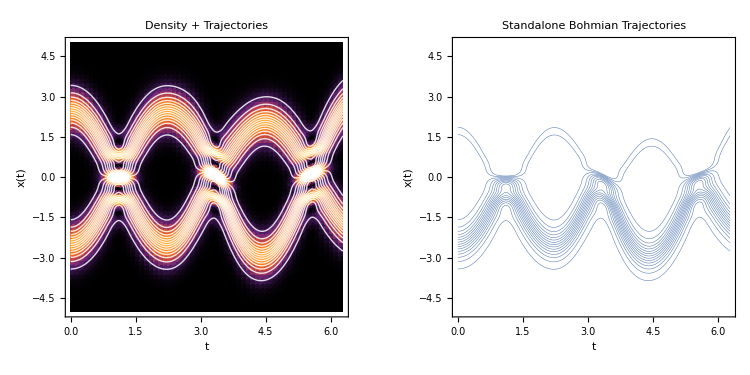

```mathematica
(*5. Side-by-side comparison:Density overlay vs.Standalone trajectory channels*)
GraphicsRow[{Show[DensityPlot[objCat["RHOX"][x,t],{t,0,2 Pi},{x,-5,5},PlotPoints->60,ColorFunction->"SunsetColors",FrameLabel->{"t","x(t)"},PlotLabel->"Density + Trajectories"],ListLinePlot[trajCat,PlotStyle->Directive[White,Opacity[0.85],Thin]]],ListLinePlot[trajCat,PlotRange->{{0,2 Pi},{-5,5}},PlotStyle->Directive[ColorData[97,1],Thickness[.001]],Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"Standalone Bohmian Trajectories",AspectRatio->1]},ImageSize->750]
```

Because Bohmian trajectories conserve cumulative probability along the flow, specifying a narrow probability interval “Grid” -> {N, {cMin, cMax}} in “InverseC” acts as a microscope on an individual interference feature.

Due to the dipole laser pulse V_1(t), the interference fringes are shifted both in time and position relative to an unperturbed harmonic oscillator. Below, we sample 50 trajectories inside the quantile band c∈[0.15,0.30] at t=0.9 and propagate across the short window t∈[0.9,1.3] over x∈[-0.75,0], resolving the sharp hyperbolic bifurcation and rapid velocity shear right around a single destructive node:

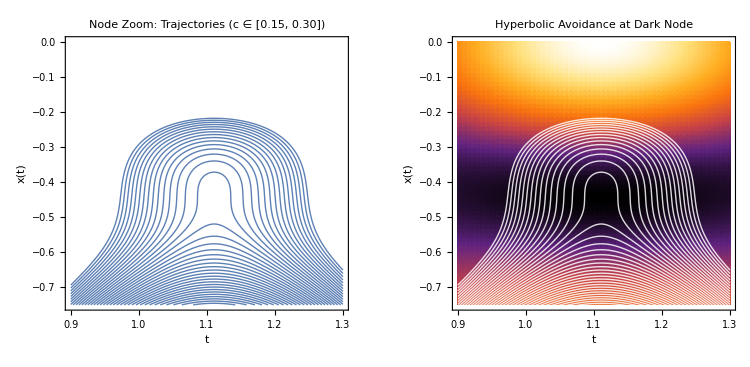

```mathematica
(*1. Sample 50 trajectories inside the quantile band c in[0.15,0.30] at t=0.9*)x0Zoom=GWPEnsemble[objCat,"SamplingMethod"->"InverseC","Grid"->{50,{0.15,0.30}},"Time"->0.9]//Chop;

(*2. Propagate over the short interference window t in[0.9,1.3]*)
solZoom=GWPEnsembleSolve[objCat,x0Zoom,{t,0.9,1.3},MaxStepSize->0.005];
parsedZoom=GWPEnsembleParse[x0Zoom,solZoom];
trajZoom=GWPEnsembleFormat[parsedZoom,"X0DAT"];

(*3. Compare standalone zoomed trajectories alongside the local node density*)
GraphicsRow[{ListLinePlot[trajZoom,PlotRange->{{0.9,1.3},{-0.75,0}},PlotStyle->Directive[ColorData[97,1],Thin],Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"Node Zoom: Trajectories (c ∈ [0.15, 0.30])",AspectRatio->1],Show[DensityPlot[objCat["RHOX"][x,t],{t,0.9,1.3},{x,-0.75,0},PlotPoints->60,ColorFunction->"SunsetColors",FrameLabel->{"t","x(t)"},PlotLabel->"Hyperbolic Avoidance at Dark Node"],ListLinePlot[trajZoom,PlotStyle->Directive[White,Opacity[0.85],Thin]]]},ImageSize->750]
```

### Parametric Resonance & Kapitza Pendulum in a 1D Paul Trap (MC1D / SS1D)

In an RF Paul trap, the quadratic curvature

V_2(t)=u_DC+u_AC cos(Ω t)

oscillates rapidly in time according to the Mathieu equation. A 3-packet “MC1D” superposition inside a modulated Paul trap exhibits rapid micromotion ripples superimposed on slow secular macromotion, while quantum interference nodes weave between the micromotion oscillations:

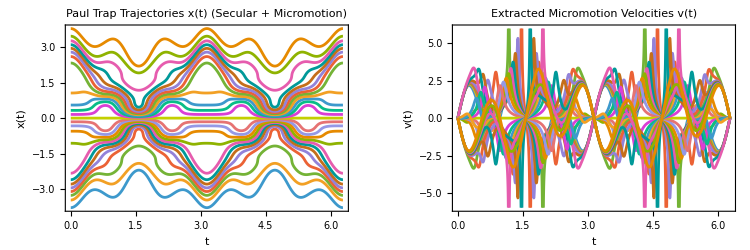

```mathematica
(*1. Paul trap curvature:DC confinement+high-frequency AC micromotion drive*)
GWPClearCache["Quiet"];
Clear[v0Paul,v1Paul,v2Paul];
v0Paul[t_]:=0;
v1Paul[t_]:=0;
v2Paul[t_]:=0.4+1.8*Cos[6 t]; (*Mathieu stability regime*)

(*2. 3-state superposition in the Paul trap*)
objPaul=GWP["MC1D"][{1,1,1},{-3,0,3},{0,0,0},"C"->{1,1,1},"Potential"->{"Numerical",v0Paul,v1Paul,v2Paul,0,2 Pi}];

(*3. Sample 25 quantile trajectories and propagate directly from objPaul*)
x0Paul=GWPEnsemble[objPaul,"SamplingMethod"->"InverseC","Grid"->25,"Time"->0];
solPaul=GWPEnsembleSolve[objPaul,x0Paul,{t,0,2 Pi},MaxStepSize->0.02];

(*4. Parse and extract both positions (X0DAT) and micromotion velocities (X1DAT)*)
parsedPaul=GWPEnsembleParse[x0Paul,solPaul];
trajPaul=GWPEnsembleFormat[parsedPaul,"X0DAT"];
velPaul=GWPEnsembleFormat[parsedPaul,"X1DAT"];

GraphicsRow[{ListLinePlot[trajPaul,Frame->True,FrameLabel->{"t","x(t)"},PlotLabel->"Paul Trap Trajectories x(t) (Secular + Micromotion)"],ListLinePlot[velPaul,Frame->True,FrameLabel->{"t","v(t)"},PlotLabel->"Extracted Micromotion Velocities v(t)"]},ImageSize->750]
```

By passing “PairWithTime” → False to GWPEnsembleFormat, we can pair the raw position and velocity time series into parametric Bohmian phase-space orbits {x(t),v(t)}.

In phase space, an individual trajectory (psPaul[[3]], left) traces a slow secular macro-orbit decorated with rapid RF micromotion oscillations and sharp vertical velocity excursions where it encounters interference nodes. Grouping the ensemble into the left (1 ;; 8), center (9 ;; 17), and right (18 ;; 25) wavepacket quantiles (right) reveals how Bohmian non-crossing confines each packet’s probability bundle to its own phase-space domain:

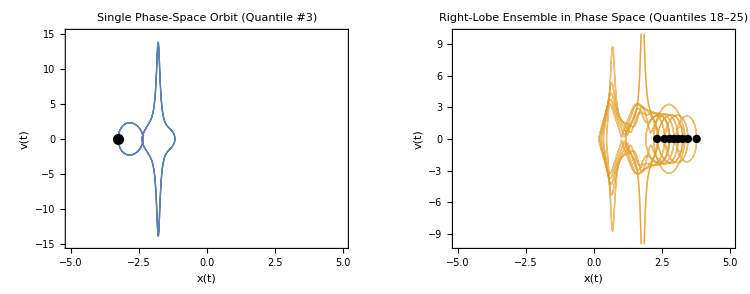

```mathematica
(*Extract un-paired x(t) and v(t) arrays and pair into {x(t),v(t)} phase-space orbits*)xRaw=GWPEnsembleFormat[parsedPaul,"X0DAT","PairWithTime"->False];
vRaw=GWPEnsembleFormat[parsedPaul,"X1DAT","PairWithTime"->False];
psPaul=MapThread[Transpose[{#1,#2}]&,{xRaw,vRaw}];

GraphicsRow[{(*Left:Single outer trajectory showing RF micromotion loops+quantum node kicks*)ListLinePlot[psPaul[[3]],PlotRange->{{-5,5},{-15,15}},PlotStyle->Directive[ColorData[97,1],Thin],Frame->True,FrameLabel->{"x(t)","v(t)"},PlotLabel->"Single Phase-Space Orbit (Quantile #3)",AspectRatio->3/4,Epilog->{PointSize[0.02],Black,Point[psPaul[[3,1]]]}],(*Right:Outer right-lobe packet bundle (quantiles 18..25) in phase space*)ListLinePlot[psPaul[[-8;;-1]],PlotRange->{{-5,5},{-10,10}},PlotStyle->Directive[ColorData[97,2],Opacity[0.65],Thin],Frame->True,FrameLabel->{"x(t)","v(t)"},PlotLabel->"Right-Lobe Ensemble in Phase Space (Quantiles 18–25)",AspectRatio->3/4,Epilog->{PointSize[0.015],Black,Point[psPaul[[-8;;-1,1]]]}]},ImageSize->750]
```

### Rotating Quadrupole / Circularly Polarized Laser Trap (“2D” Numerical Potential)

For “2D” systems, the “Numerical” potential accepts six time-dependent scalar coefficient functions defining the general locally quadratic 2D potential surface:

V(x,y,t)=V_00(t)+V_10(t)x+V_01(t)y+V_20(t)x^2+V_02(t)y^2+V_11(t)x y

Here, the linear coefficients {V_10(t),V_01(t)} represent a circularly polarized dipole laser pulse with amplitude f_0, envelope frequency ω_env, and carrier frequency ω_L:

V_10(t)=f_0 sin^2(ω_env t)cos(ω_L t)

V_01(t)=f_0 sin^2(ω_env t)sin(ω_L t)

The quadratic coefficients {V_20(t),V_02(t),V_11(t)} and anisotropic harmonic trap with base frequency ω_0 and eccentricity 0<ϵ<1 rotating at frequency Ω_Q:

V_20(t)=1/2 ω_0^2(1+ϵ cos(Ω_Q t))

V_02(t)=1/2 ω_0^2(1-ϵ cos(Ω_Q t))

V_11(t)=ω_0^2 ϵ sin(Ω_Q t))

Depending on the ratio of the quadrupole rotation rate Ω_Q to the trap frequency ω_0, the wavepacket exhibits three distinct dynamical regimes (you can switch between them by uncommenting the desired parameter block below):

Bounded Adiabatic Precession (ω_0=2.0, Ω_Q=1.0): The wavepacket breathes and precesses stably inside the rotating saddle while being spiraled by the circularly polarized laser field.

Pure Rotating Quadrupole Vortex (f_0=0, ω_0=1.5, Ω_Q=1.0): Without dipole driving, the rotating anisotropy induces pure quadrupolar shearing and vortex-like circulation.

2:1 Parametric Resonance (Ω_Q=2 ω_0): Driving the quadrupole rotation at twice the natural trap frequency excites exponential parametric amplification along the unstable manifold.

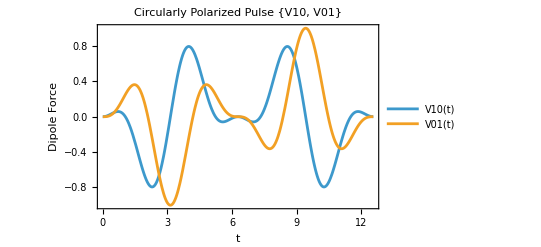

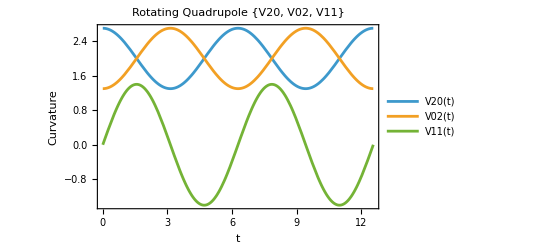

```mathematica
(*1. Clear numerical cache and previous symbol definitions*)
GWPClearCache["Quiet"];
Clear[v00,v10,v01,v20,v02,v11,f0,wEnv,wL,w0,eps,wQ];

(*---Adjustable Potential Parameters (Uncomment one regime)---*)

(*Regime A:Bounded adiabatic precession (Active Default)*)
wEnv=1/2;w0=2.0;eps=0.35;wQ=1.0;f0=1.0;wL=1.5;

(*Regime B:Pure rotating quadrupole vortex*)
(*wEnv=1/2;w0=1.5;eps=0.45;wQ=1.0;f0=0.0;wL=1.5;*)

(*Regime C:2:1 Parametric resonance blow-up*)
(*wEnv=1/2;w0=1.0;eps=0.50;wQ=2*w0;f0=1.0;wL=1.5;*)

(*2. Define the 6 scalar 2D potential coefficients*)
v00[t_]:=0;
v10[t_]:=f0*Sin[wEnv*t]^2*Cos[wL*t];
v01[t_]:=f0*Sin[wEnv*t]^2*Sin[wL*t];
v20[t_]:=(1/2)*w0^2*(1+eps*Cos[wQ*t]);
v02[t_]:=(1/2)*w0^2*(1-eps*Cos[wQ*t]);
v11[t_]:=w0^2*eps*Sin[wQ*t];

(*Inspect the dipole laser components and rotating quadrupole curvatures*)
Plot[{v10[t],v01[t]},{t,0,2*2 Pi},Frame->True,FrameLabel->{"t","Dipole Force"},PlotLabel->"Circularly Polarized Pulse {V10, V01}",PlotLegends->{"V10(t)","V01(t)"}]
Plot[{v20[t],v02[t],v11[t]},{t,0,2*2 Pi},Frame->True,FrameLabel->{"t","Curvature"},PlotLabel->"Rotating Quadrupole {V20, V02, V11}",PlotLegends->{"V20(t)","V02(t)","V11(t)"}]
```

Passing obj2DNum directly to GWPEnsembleSolve propagates the 25-trajectory “PolarC” ensemble (2×12+1 core point) without manual array transpositions:

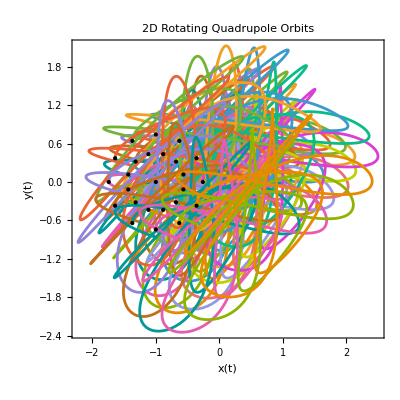

```mathematica
(*3. Construct 2D numerical wavepacket with all 6 scalar coefficient functions*)obj2DNum=GWP["2D"][{{1,0},{0,1}},{-1,0},{0,1},"Potential"->{"Numerical",v00,v10,v01,v20,v02,v11,0,2*2 Pi}];

(*4. Sample a 2D PolarC ring ensemble (2 shells x 12 rays+1 core=25 trajectories)*)
xy0Num=GWPEnsemble[obj2DNum,"SamplingMethod"->"PolarC","Grid"->{2,12},"Time"->0];

(*5. Propagate 2D Bohmian trajectories directly from obj2DNum*)
sol2DNum=GWPEnsembleSolve[obj2DNum,xy0Num,{t,0,2*2 Pi}];
parsed2DNum=GWPEnsembleParse[xy0Num,sol2DNum];
traj2DNum=GWPEnsembleFormat[parsed2DNum,"X0DAT"];

(*6. Prepend TDAT to form 3D spacetime worldlines {t,x(t),y(t)}*)
worldlines3D=MapThread[Prepend,{#,parsed2DNum["TDAT"]}]&/@traj2DNum;

GraphicsRow[{ListLinePlot[traj2DNum,AspectRatio->1,Frame->True,FrameLabel->{"x(t)","y(t)"},PlotLabel->"2D Rotating Quadrupole Orbits",Epilog->{PointSize[Small],Black,Point[xy0Num]}],ListLinePlot3D[worldlines3D,BoxRatios->{2,1,1},PlotStyle->Directive[Thick],Axes->True,AxesLabel->{"t","x(t)","y(t)"},PlotLabel->"Spacetime Worldlines (t, x, y)"]},ImageSize->780]
```

Using parsed2DNum[“TDAT”] and traj2DNum, we can animate the ensemble’s “comet tails” riding inside the rotating and breathing probability density contours. Finally, we verify that integrating the 2nd-order 2D Newton–Bohm acceleration field (combining the analytical classical force -∇V, the 2D quantum force obj2DNum[“QFX”], and obj2DNum[“MASS”]) reproduces the 1st-order Bohmian trajectories to within ∼10^-6:

```mathematica
(*Interactive comet-tail animation over the solver time grid*)
tGrid=parsed2DNum["TDAT"];

Manipulate[Module[{tNow=tGrid[[k]],tailStart=Max[1,k-15]},Show[ContourPlot[Evaluate[obj2DNum["RHOX"][x,y,tNow]],{x,-3.5,3.5},{y,-3.5,3.5},Contours->8,ColorFunction->"DeepSeaColors",PlotRange->All,Exclusions->None],Graphics[{(*Fading comet tails over the last 15 solver time steps*)White,Opacity[0.7],Thick,Line[traj2DNum[[All,tailStart;;k]]],(*Current particle positions*)Yellow,PointSize[Medium],Point[traj2DNum[[All,k]]]}],Frame->True,FrameLabel->{"x","y"},PlotLabel->Row[{"t = ",NumberForm[tNow,{4,2}]}],ImageSize->420]],{{k,1,"Time Step"},1,Length[tGrid],1,Animator}]
```

```mathematica
(*---2nd-Order 2D Newton-Bohm Verification---*)(*1. Initial 2D velocities at t=0*)vxy0Num=Transpose@obj2DNum["VX"][xy0Num[[All,1]],xy0Num[[All,2]],0];

(*2. Total 2D acceleration:(F_external+F_quantum)/Mass directly from obj2DNum*)
fTotal2D[xy_,t_]:=Module[{x=xy[[All,1]],y=xy[[All,2]]},Transpose[obj2DNum["FEX"][x,y,t]+obj2DNum["QFX"][x,y,t]]/obj2DNum["MASS"]];

(*3. Integrate 2nd-order 2D Newton-Bohm equations*)
sol2DNum2nd=GWPEnsembleSolve[xy0Num,vxy0Num,fTotal2D,{t,0,2 Pi}];

(*4. Maximum 2D endpoint discrepancy between 1st-order and 2nd-order propagation at t=2 Pi*)
Max@Abs[Through[sol2DNum[2 Pi]]-Through[sol2DNum2nd[2 Pi]]]
```

1.63391×10^-6